### Gamma

```mathematica
(* looping over Mathematica files *)
SetDirectory[NotebookDirectory[]]
```

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran

```mathematica
(* available result directories *)
dirNames=Join[FileNames["./dim*"][[24;;51]],FileNames["./dim*"][[52;;70]],
Table["./dim"<>ToString[NumberForm[i,{5,4}]],{i,4.4,4.79,0.01}]
]
```

{./dim3.2000,./dim3.2500,./dim3.3000,./dim3.3500,./dim3.4000,./dim3.4500,./dim3.5000,./dim3.5500,./dim3.6000,./dim3.6500,./dim3.7000,./dim3.7100,./dim3.7200,./dim3.7300,./dim3.7400,./dim3.7500,./dim3.7550,./dim3.7554,./dim3.7555,./dim3.7556,./dim3.7557,./dim3.75572,./dim3.755726,./dim3.7557262,./dim3.75572621,./dim3.75572622,./dim3.75572623,./dim3.75573,./dim3.7558,./dim3.7559,./dim3.7560,./dim3.7600,./dim3.7700,./dim3.7800,./dim3.7900,./dim3.8000,./dim3.8500,./dim3.9000,./dim3.9500,./dim4.0000,./dim4.0500,./dim4.1000,./dim4.1500,./dim4.2000,./dim4.2500,./dim4.3000,./dim4.3500,./dim4.4000,./dim4.4100,./dim4.4200,./dim4.4300,./dim4.4400,./dim4.4500,./dim4.4600,./dim4.4700,./dim4.4800,./dim4.4900,./dim4.5000,./dim4.5100,./dim4.5200,./dim4.5300,./dim4.5400,./dim4.5500,./dim4.5600,./dim4.5700,./dim4.5800,./dim4.5900,./dim4.6000,./dim4.6100,./dim4.6200,./dim4.6300,./dim4.6400,./dim4.6500,./dim4.6600,./dim4.6700,./dim4.6800,./dim4.6900,./dim4.7000,./dim4.7100,./dim4.7200,./dim4.7300,./dim4.7400,./dim4.7500,./dim4.7600,./dim4.7700,./dim4.7800,./dim4.7900}

```mathematica
dirNames256=Table["./dim"<>ToString[NumberForm[i,{5,4}]],{i,4.8,4.97,0.005}]
```

{./dim4.8000,./dim4.8050,./dim4.8100,./dim4.8150,./dim4.8200,./dim4.8250,./dim4.8300,./dim4.8350,./dim4.8400,./dim4.8450,./dim4.8500,./dim4.8550,./dim4.8600,./dim4.8650,./dim4.8700,./dim4.8750,./dim4.8800,./dim4.8850,./dim4.8900,./dim4.8950,./dim4.9000,./dim4.9050,./dim4.9100,./dim4.9150,./dim4.9200,./dim4.9250,./dim4.9300,./dim4.9350,./dim4.9400,./dim4.9450,./dim4.9500,./dim4.9550,./dim4.9600,./dim4.9650,./dim4.9700}

```mathematica
(* gamma of D *)
gList=Table[{dimNow=Import[dirNames[[i]]<>"/512/pert/shoot_inner.par","Table"][[2,1]],gNow=Get[dirNames[[i]]<>"/512/pert/gam.out"]}
,{i,Length[dirNames]}]
```

{{3.2,0.248607},{3.25,0.266031},{3.3,0.280714},{3.35,0.293303},{3.4,0.304247},{3.45,0.313862},{3.5,0.322386},{3.55,0.329998},{3.6,0.336841},{3.65,0.343028},{3.7,0.34865},{3.71,0.349714},{3.72,0.350758},{3.73,0.351784},{3.74,0.352792},{3.75,0.353783},{3.755,0.354272},{3.7554,0.354311},{3.7555,0.35432},{3.7556,0.35433},{3.7557,0.35434},{3.75572,0.354342},{3.75573,0.354342},{3.75573,0.354342},{3.75573,0.354342},{3.75573,0.354342},{3.75573,0.354342},{3.75573,0.354343},{3.7558,0.35435},{3.7559,0.354359},{3.756,0.354369},{3.76,0.354756},{3.77,0.355713},{3.78,0.356654},{3.79,0.357579},{3.8,0.358488},{3.85,0.362818},{3.9,0.366816},{3.95,0.370519},{4.,0.373961},{4.05,0.377167},{4.1,0.380162},{4.15,0.382966},{4.2,0.385598},{4.25,0.388074},{4.3,0.390406},{4.35,0.392609},{4.4,0.394692},{4.41,0.395095},{4.42,0.395494},{4.43,0.395889},{4.44,0.39628},{4.45,0.396666},{4.46,0.397048},{4.47,0.397427},{4.48,0.397801},{4.49,0.398172},{4.5,0.398539},{4.51,0.398902},{4.52,0.399262},{4.53,0.399618},{4.54,0.399971},{4.55,0.40032},{4.56,0.400665},{4.57,0.401007},{4.58,0.401346},{4.59,0.401682},{4.6,0.402014},{4.61,0.402343},{4.62,0.402669},{4.63,0.402992},{4.64,0.403312},{4.65,0.403629},{4.66,0.403944},{4.67,0.404255},{4.68,0.404563},{4.69,0.404868},{4.7,0.405171},{4.71,0.405471},{4.72,0.405769},{4.73,0.406063},{4.74,0.406355},{4.75,0.406645},{4.76,0.406931},{4.77,0.407216},{4.78,0.407497},{4.79,0.407776}}

```mathematica
Export["gamma.dat",gList]
```

gamma.dat

```mathematica
(* results in Blands thesis *)
gammaBT={
{3.02,0.1379,0.0042},
{3.05,0.1628,0.0008},
{3.1,0.1989,0.0014},
{3.2,0.2495,0.0010},
{3.3,0.2853,0.0024},
{3.4,0.3053,0.0027},
{3.5,0.3235,0.0018},
{3.7,0.3476,0.0015},
{3.9,0.3672,0.0023},
{4.0,0.3744,0.0022}
};
Export["gBlandThesis.dat",gammaBT]
```

gBlandThesis.dat

```mathematica
(* results in Blands paper Table 1 https://arxiv.org/pdf/gr-qc/0507088 *)
gammaB1={
{3.5,0.349,0.003},
{4,0.374,0.002},
{5,0.412,0.004},
{6,0.430,0.003},
{7,0.441,0.004},
{8,0.446,0.004},
{9,0.452,0.003},
{10,0.456,0.004},
{11,0.459,0.004},
{12,0.462,0.005},
{13,0.463,0.004},
{14,0.465,0.004}
};
Export["gBlandPaper1.dat",gammaB1]
```

gBlandPaper1.dat

```mathematica
(* results in Blands paper Table 1 https://arxiv.org/pdf/hep-th/0702226 *)
gammaB2={
{5,0.4131,0.0001}
};
Export["gBlandPaper2.dat",gammaB2]
```

gBlandPaper2.dat

```mathematica
(* results in Gaume paper abstract https://arxiv.org/pdf/hep-th/0611312 *)
gammaAG1={
{5,0.412,0.004}
};
Export["gAlvarez.dat",gammaAG1]
```

gAlvarez.dat

```mathematica
(* results in Sorkin paper Table 1 https://arxiv.org/pdf/hep-th/0502034 *)
gammaSO={
{4,0.372,0.004},
{5,0.408,0.008},
{6,0.422,0.008},
{7,0.429,0.009},
{8,0.436,0.009},
{9,0.442,0.009},
{10,0.447,0.013},
{11,0.44,0.013}
};
Export["gSorkin.dat",gammaSO]
```

gSorkin.dat

```mathematica
gammaInt=Interpolation[Thread[{gammaBT[[;;,1]],gammaBT[[;;,2]]}]];
gammaIntplus=Interpolation[Thread[{gammaBT[[;;,1]],gammaBT[[;;,2]]+gammaBT[[;;,3]]}]];
gammaIntminus=Interpolation[Thread[{gammaBT[[;;,1]],gammaBT[[;;,2]]-gammaBT[[;;,3]]}]];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

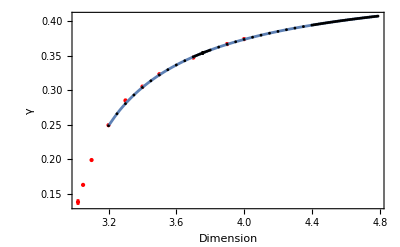

```mathematica
fitFun[ϵ_]:=a+b*(ϵ-3);
FitData=Thread[{gammaBT[[1;;3,1]],gammaBT[[1;;3,2]]}];
FitDataPlus=Thread[{gammaBT[[1;;3,1]],gammaBT[[1;;3,2]]+gammaBT[[1;;3,3]]}];
FitDataMinus=Thread[{gammaBT[[1;;3,1]],gammaBT[[1;;3,2]]-gammaBT[[1;;3,3]]}];
fitRes=FindFit[FitData,fitFun[ϵ],{a,b},ϵ];
fitResPlus=FindFit[FitDataPlus,fitFun[ϵ],{a,b},ϵ];
fitResMinus=FindFit[FitDataMinus,fitFun[ϵ],{a,b},ϵ];
Needs["ErrorBarPlots`"]
gammaDataPlot=ErrorListPlot[Table[{{gammaBT[[i,1]],gammaBT[[i,2]]},ErrorBar[gammaBT[[i,3]]]},{i,1,Length[gammaBT]}],PlotRange->{{3,4.9},All},ImageSize->400,PlotStyle->{PointSize[Small],Red},FrameLabel->{"Dimension","γ"},LabelStyle->{Black,12},AxesOrigin->{3.0,0.1},Frame->True];
Show[gammaDataPlot,
ListPlot[gList,Joined->True,Frame->True,FrameLabel->{"Dimension","γ"},InterpolationOrder->2],
ListPlot[gList,Joined->False,Frame->True,FrameLabel->{"Dimension","γ"},PlotStyle->{{Black,PointSize[0.005]}}],
PlotRange->All,Frame->True
]
```

### Delta

```mathematica
(* results in Blands thesis *)
deltaBT={
{3.02,2.083,0.024},
{3.05,2.526,0.025},
{3.1,2.783,0.015},
{3.2,3.097,0.011},
{3.3,3.254,0.019},
{3.4,3.354,0.016},
{3.5,3.411,0.017},
{3.7,3.451,0.013},
{3.9,3.453,0.014},
{4.0,3.445,0.013}
};
Export["DeltaBlandThesis.dat",deltaBT]
```

DeltaBlandThesis.dat

```mathematica
(* results in Blands paper Table 1 https://arxiv.org/pdf/gr-qc/0507088 *)
deltaB1={
{4,3.4,0.1},
{5,3.1,0.1},
{6,2.98,0.1},
{7,2.96,0.1},
{8,2.77,0.1},
{9,2.63,0.1},
{10,2.5,0.1},
{11,2.46,0.1},
{12,2.44,0.1},
{13,2.40,0.1}
};
Export["DeltaBlandPaper1.dat",deltaB1]
```

DeltaBlandPaper1.dat

```mathematica
(* results in Blands paper Table 1 https://arxiv.org/pdf/hep-th/0702226 *)
deltaB2={
{5,3.2246,0.0005}
};
Export["DeltaBlandPaper2.dat",deltaB2]
```

DeltaBlandPaper2.dat

```mathematica
(* results in Sorkin paper Table 1 https://arxiv.org/pdf/hep-th/0502034 *)
deltaSO={
{4,3.37,3.37*0.02},
{5,3.19,3.19*0.02},
{6,3.01,3.01*0.02},
{7,2.83,2.83*0.02},
{8,2.70,2.7*0.02},
{9,2.61,2.61*0.03},
{10,2.55,2.55*0.03},
{11,2.51,2.51*0.03}
};
Export["DeltaSorkin.dat",deltaSO]
```

DeltaSorkin.dat

```mathematica
(* available result directories *)
SetDirectory[NotebookDirectory[]];
dirNames=Join[FileNames["./dim*"][[24;;44]],FileNames["./dim*"][[52;;68]]]
(* gamma of D *)
deltaList1=Table[{dimNow=Import[dirNames[[i]]<>"/512/pert/shoot_inner.par","Table"][[2,1]],Get[dirNames[[i]]<>"/512/pert/Delta.out"]}
,{i,Length[dirNames]}];
(* inaccurate small D results with 512 modes *)
dirNames=FileNames["./dim*"][[11;;25]]
(* gamma of D *)
deltaList2=Table[{dimNow=Import[dirNames[[i]]<>"/512/shoot_inner.par","Table"][[2,1]],Get[dirNames[[i]]<>"/512/Delta.out"]}
,{i,Length[dirNames]}];
(* large D with 128 modes *)
dirNames=FileNames["./dim*"][[68;;272]]
(* gamma of D *)
deltaList3=Table[{dimNow=Import[dirNames[[i]]<>"/128/shoot_inner.par","Table"][[2,1]],Get[dirNames[[i]]<>"/128/Delta.out"]}
,{i,Length[dirNames]}];
(* large D with 128 modes *)
dirNames=FileNames["./dim*"][[273;;-1]]
(* gamma of D *)
deltaList4=Table[{dimNow=Import[dirNames[[i]]<>"/256/shoot_inner.par","Table"][[2,1]],Get[dirNames[[i]]<>"/256/Delta.out"]}
,{i,Length[dirNames]}];

(* combining into one list *)
deltaList=Join[deltaList2,deltaList1,deltaList3,deltaList4];
```

{./dim3.2000,./dim3.2500,./dim3.3000,./dim3.3500,./dim3.4000,./dim3.4500,./dim3.5000,./dim3.5500,./dim3.6000,./dim3.6500,./dim3.7000,./dim3.7100,./dim3.7200,./dim3.7300,./dim3.7400,./dim3.7500,./dim3.7550,./dim3.7554,./dim3.7555,./dim3.7556,./dim3.7557,./dim3.7558,./dim3.7559,./dim3.7560,./dim3.7600,./dim3.7700,./dim3.7800,./dim3.7900,./dim3.8000,./dim3.8500,./dim3.9000,./dim3.9500,./dim4.0000,./dim4.0500,./dim4.1000,./dim4.1500,./dim4.2000,./dim4.2500}

{./dim3.1200,./dim3.1250,./dim3.1300,./dim3.1350,./dim3.1400,./dim3.1450,./dim3.1500,./dim3.1550,./dim3.1600,./dim3.1650,./dim3.1700,./dim3.1750,./dim3.1800,./dim3.2000,./dim3.2500}

{./dim4.2500,./dim4.3000,./dim4.3500,./dim4.3550,./dim4.3600,./dim4.3650,./dim4.3700,./dim4.3750,./dim4.3800,./dim4.3850,./dim4.3900,./dim4.3950,./dim4.4000,./dim4.4050,./dim4.4100,./dim4.4150,./dim4.4200,./dim4.4250,./dim4.4300,./dim4.4350,./dim4.4400,./dim4.4450,./dim4.4500,./dim4.4550,./dim4.4600,./dim4.4650,./dim4.4700,./dim4.4750,./dim4.4800,./dim4.4850,./dim4.4900,./dim4.4950,./dim4.5000,./dim4.5050,./dim4.5100,./dim4.5150,./dim4.5200,./dim4.5250,./dim4.5300,./dim4.5350,./dim4.5400,./dim4.5450,./dim4.5500,./dim4.5550,./dim4.5600,./dim4.5650,./dim4.5700,./dim4.5750,./dim4.5800,./dim4.5850,./dim4.5900,./dim4.5950,./dim4.6000,./dim4.6050,./dim4.6100,./dim4.6150,./dim4.6160,./dim4.6200,./dim4.6220,./dim4.6250,./dim4.6280,./dim4.6300,./dim4.6320,./dim4.6340,./dim4.6360,./dim4.6380,./dim4.6400,./dim4.6420,./dim4.6440,./dim4.6460,./dim4.6480,./dim4.6500,./dim4.6520,./dim4.6540,./dim4.6560,./dim4.6580,./dim4.6600,./dim4.6620,./dim4.6640,./dim4.6650,./dim4.6660,./dim4.6670,./dim4.6680,./dim4.6690,./dim4.6700,./dim4.6710,./dim4.6720,./dim4.6730,./dim4.6740,./dim4.6750,./dim4.6760,./dim4.6770,./dim4.6780,./dim4.6790,./dim4.6800,./dim4.6810,./dim4.6820,./dim4.6830,./dim4.6840,./dim4.6850,./dim4.6860,./dim4.6870,./dim4.6880,./dim4.6890,./dim4.6900,./dim4.6910,./dim4.6920,./dim4.6930,./dim4.6940,./dim4.6950,./dim4.6960,./dim4.6970,./dim4.6980,./dim4.6990,./dim4.7000,./dim4.7010,./dim4.7020,./dim4.7030,./dim4.7040,./dim4.7050,./dim4.7060,./dim4.7070,./dim4.7080,./dim4.7090,./dim4.7100,./dim4.7110,./dim4.7120,./dim4.7130,./dim4.7140,./dim4.7150,./dim4.7160,./dim4.7170,./dim4.7180,./dim4.7190,./dim4.7200,./dim4.7210,./dim4.7220,./dim4.7230,./dim4.7240,./dim4.7250,./dim4.7260,./dim4.7270,./dim4.7280,./dim4.7290,./dim4.7300,./dim4.7310,./dim4.7320,./dim4.7330,./dim4.7340,./dim4.7350,./dim4.7360,./dim4.7370,./dim4.7380,./dim4.7390,./dim4.7400,./dim4.7410,./dim4.7420,./dim4.7430,./dim4.7440,./dim4.7450,./dim4.7460,./dim4.7470,./dim4.7480,./dim4.7490,./dim4.7500,./dim4.7510,./dim4.7520,./dim4.7530,./dim4.7540,./dim4.7550,./dim4.7560,./dim4.7570,./dim4.7580,./dim4.7590,./dim4.7600,./dim4.7610,./dim4.7620,./dim4.7630,./dim4.7640,./dim4.7650,./dim4.7660,./dim4.7670,./dim4.7680,./dim4.7690,./dim4.7700,./dim4.7710,./dim4.7720,./dim4.7730,./dim4.7740,./dim4.7750,./dim4.7760,./dim4.7770,./dim4.7780,./dim4.7790,./dim4.7800,./dim4.7810,./dim4.7820,./dim4.7830,./dim4.7840,./dim4.7850,./dim4.7860,./dim4.7870,./dim4.7880,./dim4.7890,./dim4.7900}

{./dim4.8000,./dim4.8050,./dim4.8100,./dim4.8150,./dim4.8200,./dim4.8250,./dim4.8300,./dim4.8350,./dim4.8400,./dim4.8450,./dim4.8500,./dim4.8550,./dim4.8600,./dim4.8650,./dim4.8700,./dim4.8750,./dim4.8800,./dim4.8850,./dim4.8900,./dim4.8950,./dim4.9000,./dim4.9050,./dim4.9100,./dim4.9150,./dim4.9200,./dim4.9250,./dim4.9300,./dim4.9350,./dim4.9400,./dim4.9450,./dim4.9500,./dim4.9550,./dim4.9600,./dim4.9650,./dim4.9700,./dim4.9750,./dim4.9800,./dim4.9850,./dim4.9900,./dim4.9950}

```mathematica
7
```

```mathematica
deltaList
```

{{3.12,2.85383},{3.125,2.87338},{3.13,2.89214},{3.135,2.91016},{3.14,2.92749},{3.145,2.94418},{3.15,2.96027},{3.155,2.9758},{3.16,2.9908},{3.165,3.00529},{3.17,3.0193},{3.175,3.03286},{3.18,3.04599},{3.2,3.09452},{3.25,3.1931},{3.2,3.09474},{3.25,3.19315},{3.3,3.26721},{3.35,3.32346},{3.4,3.36625},{3.45,3.39862},{3.5,3.42279},{3.55,3.4404},{3.6,3.45272},{3.65,3.46073},{3.7,3.4652},{3.71,3.46573},{3.72,3.46614},{3.73,3.46645},{3.74,3.46665},{3.75,3.46676},{3.755,3.46677},{3.7554,3.46677},{3.7555,3.46677},{3.7556,3.46677},{3.7557,3.46677},{3.7558,3.46677},{3.7559,3.46677},{3.756,3.46677},{3.76,3.46676},{3.77,3.46668},{3.78,3.4665},{3.79,3.46624},{3.8,3.4659},{3.85,3.46303},{3.9,3.45849},{3.95,3.45255},{4.,3.44545},{4.05,3.43738},{4.1,3.4285},{4.15,3.41895},{4.2,3.40884},{4.25,3.39827},{4.25,3.39827},{4.3,3.38734},{4.35,3.3761},{4.355,3.37496},{4.36,3.37382},{4.365,3.37268},{4.37,3.37153},{4.375,3.37038},{4.38,3.36923},{4.385,3.36808},{4.39,3.36693},{4.395,3.36577},{4.4,3.36462},{4.405,3.36346},{4.41,3.3623},{4.415,3.36114},{4.42,3.35997},{4.425,3.35881},{4.43,3.35764},{4.435,3.35647},{4.44,3.3553},{4.445,3.35413},{4.45,3.35295},{4.455,3.35178},{4.46,3.3506},{4.465,3.34942},{4.47,3.34824},{4.475,3.34706},{4.48,3.34588},{4.485,3.3447},{4.49,3.34352},{4.495,3.34233},{4.5,3.34115},{4.505,3.33996},{4.51,3.33877},{4.515,3.33758},{4.52,3.33639},{4.525,3.3352},{4.53,3.33401},{4.535,3.33282},{4.54,3.33163},{4.545,3.33043},{4.55,3.32924},{4.555,3.32804},{4.56,3.32685},{4.565,3.32565},{4.57,3.32446},{4.575,3.32326},{4.58,3.32206},{4.585,3.32086},{4.59,3.31966},{4.595,3.31846},{4.6,3.31727},{4.605,3.31607},{4.61,3.31487},{4.615,3.31366},{4.616,3.31342},{4.62,3.31246},{4.622,3.31198},{4.625,3.31126},{4.628,3.31054},{4.63,3.31006},{4.632,3.30958},{4.634,3.3091},{4.636,3.30862},{4.638,3.30814},{4.64,3.30766},{4.642,3.30718},{4.644,3.3067},{4.646,3.30621},{4.648,3.30573},{4.65,3.30525},{4.652,3.30477},{4.654,3.30429},{4.656,3.30381},{4.658,3.30333},{4.66,3.30285},{4.662,3.30237},{4.664,3.30189},{4.665,3.30165},{4.666,3.30141},{4.667,3.30117},{4.668,3.30092},{4.669,3.30068},{4.67,3.30044},{4.671,3.3002},{4.672,3.29996},{4.673,3.29972},{4.674,3.29948},{4.675,3.29924},{4.676,3.299},{4.677,3.29876},{4.678,3.29852},{4.679,3.29828},{4.68,3.29804},{4.681,3.2978},{4.682,3.29756},{4.683,3.29732},{4.684,3.29708},{4.685,3.29684},{4.686,3.2966},{4.687,3.29636},{4.688,3.29611},{4.689,3.29587},{4.69,3.29563},{4.691,3.29539},{4.692,3.29515},{4.693,3.29491},{4.694,3.29467},{4.695,3.29443},{4.696,3.29419},{4.697,3.29395},{4.698,3.29371},{4.699,3.29347},{4.7,3.29323},{4.701,3.29299},{4.702,3.29275},{4.703,3.29251},{4.704,3.29227},{4.705,3.29203},{4.706,3.29179},{4.707,3.29155},{4.708,3.29131},{4.709,3.29107},{4.71,3.29082},{4.711,3.29058},{4.712,3.29034},{4.713,3.2901},{4.714,3.28986},{4.715,3.28962},{4.716,3.28938},{4.717,3.28914},{4.718,3.2889},{4.719,3.28866},{4.72,3.28842},{4.721,3.28818},{4.722,3.28794},{4.723,3.2877},{4.724,3.28746},{4.725,3.28722},{4.726,3.28698},{4.727,3.28674},{4.728,3.2865},{4.729,3.28626},{4.73,3.28602},{4.731,3.28578},{4.732,3.28554},{4.733,3.2853},{4.734,3.28506},{4.735,3.28482},{4.736,3.28458},{4.737,3.28434},{4.738,3.2841},{4.739,3.28386},{4.74,3.28362},{4.741,3.28338},{4.742,3.28314},{4.743,3.2829},{4.744,3.28266},{4.745,3.28242},{4.746,3.28218},{4.747,3.28194},{4.748,3.2817},{4.749,3.28146},{4.75,3.28122},{4.751,3.28097},{4.752,3.28073},{4.753,3.28049},{4.754,3.28025},{4.755,3.28001},{4.756,3.27977},{4.757,3.27954},{4.758,3.2793},{4.759,3.27906},{4.76,3.27882},{4.761,3.27858},{4.762,3.27834},{4.763,3.2781},{4.764,3.27786},{4.765,3.27762},{4.766,3.27738},{4.767,3.27714},{4.768,3.2769},{4.769,3.27666},{4.77,3.27642},{4.771,3.27618},{4.772,3.27594},{4.773,3.2757},{4.774,3.27546},{4.775,3.27522},{4.776,3.27498},{4.777,3.27474},{4.778,3.2745},{4.779,3.27426},{4.78,3.27402},{4.781,3.27378},{4.782,3.27354},{4.783,3.2733},{4.784,3.27306},{4.785,3.27282},{4.786,3.27258},{4.787,3.27234},{4.788,3.2721},{4.789,3.27186},{4.79,3.27147},{4.8,3.26923},{4.805,3.26804},{4.81,3.26684},{4.815,3.26564},{4.82,3.26445},{4.825,3.26326},{4.83,3.26206},{4.835,3.26087},{4.84,3.25968},{4.845,3.25849},{4.85,3.2573},{4.855,3.2561},{4.86,3.25492},{4.865,3.25373},{4.87,3.25254},{4.875,3.25135},{4.88,3.25016},{4.885,3.24898},{4.89,3.24779},{4.895,3.24661},{4.9,3.24542},{4.905,3.24424},{4.91,3.24306},{4.915,3.24188},{4.92,3.24069},{4.925,3.23952},{4.93,3.23834},{4.935,3.23716},{4.94,3.23598},{4.945,3.2348},{4.95,3.23363},{4.955,3.23245},{4.96,3.23128},{4.965,3.23011},{4.97,3.22894},{4.975,3.22777},{4.98,3.2266},{4.985,3.22543},{4.99,3.22426},{4.995,3.22309}}

```mathematica
Export["Delta.dat",deltaList]
```

Delta.dat

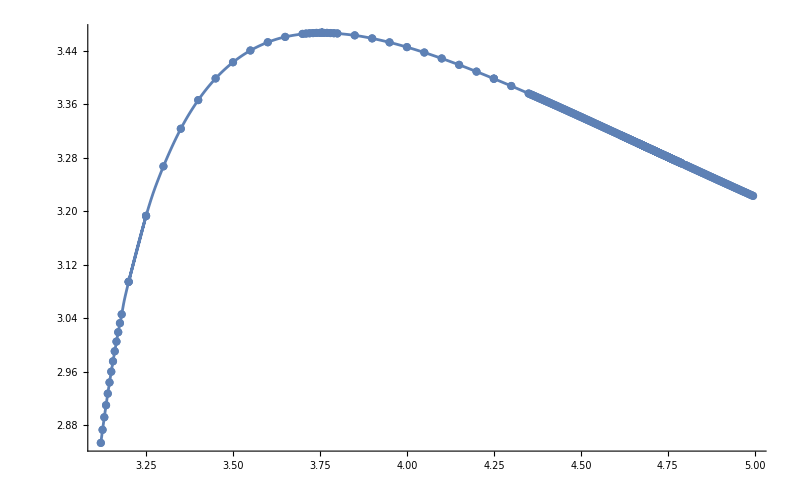

```mathematica
ListPlot[deltaList,PlotRange->All,Joined->True,InterpolationOrder->2,Mesh->Full]
```

{{3.12,2.85383},{3.125,2.87338},{3.13,2.89214},{3.135,2.91016},{3.14,2.92749},{3.145,2.94418},{3.15,2.96027},{3.155,2.9758},{3.16,2.9908},{3.165,3.00529}}

{a→3.8626,b→0.475683}

ListLogLogPlot::ioproc: {{1.13783,1.04866},{1.13943,1.05549},{1.14103,1.062},{1.14263,1.06821},{1.14422,1.07414},{1.14581,1.07983},{1.1474,1.08528},{1.14899,1.09051},«36»,{1.34807,1.24214},{1.36098,1.24083},{1.37372,1.23911},{1.38629,1.23706},{1.39872,1.23471},{1.41099,1.23212},«210»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

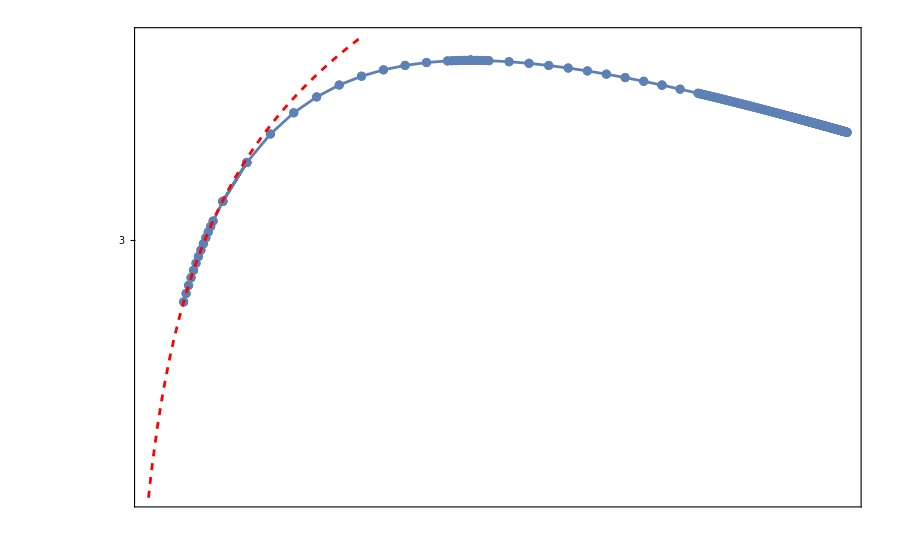

```mathematica
data=deltaList[[;;10]]
fitf=a+b Log[x-3];
fit=FindFit[data,fitf,{a,b},x]
Show[
ListLogLogPlot[deltaList,PlotRange->All,Joined->True,InterpolationOrder->2,Mesh->Full],
LogLogPlot[fitf/.fit,{x,3.05,3.5},PlotStyle->{Red,Dashed}]
,Frame->True]
```

```mathematica
(* available result directories *)
SetDirectory[NotebookDirectory[]];
dirNames=Join[FileNames["./dim*"][[24;;44]],FileNames["./dim*"][[52;;68]]]
(* gamma of D *)
deltaList1=Table[{dimNow=Import[dirNames[[i]]<>"/512/pert/shoot_inner.par","Table"][[2,1]],gNow=Get[dirNames[[i]]<>"/512/pert/Delta.out"]}
,{i,Length[dirNames]}]
```

{./dim3.2000,./dim3.2500,./dim3.3000,./dim3.3500,./dim3.4000,./dim3.4500,./dim3.5000,./dim3.5500,./dim3.6000,./dim3.6500,./dim3.7000,./dim3.7100,./dim3.7200,./dim3.7300,./dim3.7400,./dim3.7500,./dim3.7550,./dim3.7554,./dim3.7555,./dim3.7556,./dim3.7557,./dim3.7558,./dim3.7559,./dim3.7560,./dim3.7600,./dim3.7700,./dim3.7800,./dim3.7900,./dim3.8000,./dim3.8500,./dim3.9000,./dim3.9500,./dim4.0000,./dim4.0500,./dim4.1000,./dim4.1500,./dim4.2000,./dim4.2500}

{{3.2,3.09474},{3.25,3.19315},{3.3,3.26721},{3.35,3.32346},{3.4,3.36625},{3.45,3.39862},{3.5,3.42279},{3.55,3.4404},{3.6,3.45272},{3.65,3.46073},{3.7,3.4652},{3.71,3.46573},{3.72,3.46614},{3.73,3.46645},{3.74,3.46665},{3.75,3.46676},{3.755,3.46677},{3.7554,3.46677},{3.7555,3.46677},{3.7556,3.46677},{3.7557,3.46677},{3.7558,3.46677},{3.7559,3.46677},{3.756,3.46677},{3.76,3.46676},{3.77,3.46668},{3.78,3.4665},{3.79,3.46624},{3.8,3.4659},{3.85,3.46303},{3.9,3.45849},{3.95,3.45255},{4.,3.44545},{4.05,3.43738},{4.1,3.4285},{4.15,3.41895},{4.2,3.40884},{4.25,3.39827}}

```mathematica
Export["gamma.dat",gList]
```

gamma.dat

```mathematica
gamma={
{3.02,0.1379,0.0042},
{3.05,0.1628,0.0008},
{3.1,0.1989,0.0014},
{3.2,0.2495,0.0010},
{3.3,0.2853,0.0024},
{3.4,0.3053,0.0027},
{3.5,0.3235,0.0018},
{3.7,0.3476,0.0015},
{3.9,0.3672,0.0023},
{4.0,0.3744,0.0022}
};
```

```mathematica
Export["Bland.dat",gamma]
```

Bland.dat

```mathematica
gammaInt=Interpolation[Thread[{gamma[[;;,1]],gamma[[;;,2]]}]];
gammaIntplus=Interpolation[Thread[{gamma[[;;,1]],gamma[[;;,2]]+gamma[[;;,3]]}]];
gammaIntminus=Interpolation[Thread[{gamma[[;;,1]],gamma[[;;,2]]-gamma[[;;,3]]}]];
```

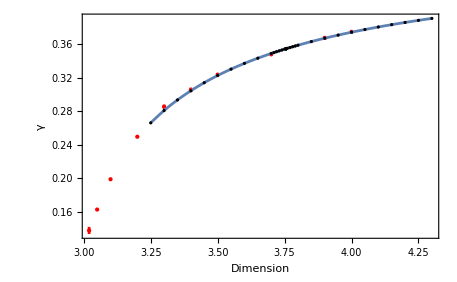

```mathematica
fitFun[ϵ_]:=a+b*(ϵ-3);
FitData=Thread[{gamma[[1;;3,1]],gamma[[1;;3,2]]}];
FitDataPlus=Thread[{gamma[[1;;3,1]],gamma[[1;;3,2]]+gamma[[1;;3,3]]}];
FitDataMinus=Thread[{gamma[[1;;3,1]],gamma[[1;;3,2]]-gamma[[1;;3,3]]}];
fitRes=FindFit[FitData,fitFun[ϵ],{a,b},ϵ];
fitResPlus=FindFit[FitDataPlus,fitFun[ϵ],{a,b},ϵ];
fitResMinus=FindFit[FitDataMinus,fitFun[ϵ],{a,b},ϵ];
Needs["ErrorBarPlots`"]
gammaDataPlot=ErrorListPlot[Table[{{gamma[[i,1]],gamma[[i,2]]},ErrorBar[gamma[[i,3]]]},{i,1,Length[gamma]}],PlotRange->{{3,4.3},All},ImageSize->400,PlotStyle->{PointSize[Small],Red},FrameLabel->{"Dimension","γ"},LabelStyle->{Black,12},AxesOrigin->{3.0,0.1},Frame->True];
Show[gammaDataPlot,
ListPlot[gList,Joined->True,Frame->True,FrameLabel->{"Dimension","γ"},InterpolationOrder->2],
ListPlot[gList,Joined->False,Frame->True,FrameLabel->{"Dimension","γ"},PlotStyle->{{Black,PointSize[0.005]}}],
PlotRange->All,Frame->True
]
```

### Plotting

```mathematica
(* looping over Mathematica files *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* available result directories *)
dirNames=FileNames["./dim*"][[11;;70]]
```

{./dim3.1200,./dim3.1250,./dim3.1300,./dim3.1350,./dim3.1400,./dim3.1450,./dim3.1500,./dim3.1550,./dim3.1600,./dim3.1650,./dim3.1700,./dim3.1750,./dim3.1800,./dim3.2000,./dim3.2500,./dim3.3000,./dim3.3500,./dim3.4000,./dim3.4500,./dim3.5000,./dim3.5500,./dim3.6000,./dim3.6500,./dim3.7000,./dim3.7100,./dim3.7200,./dim3.7300,./dim3.7400,./dim3.7500,./dim3.7550,./dim3.7554,./dim3.7555,./dim3.7556,./dim3.7557,./dim3.75572,./dim3.755726,./dim3.7557262,./dim3.75572621,./dim3.75572622,./dim3.75572623,./dim3.75573,./dim3.7558,./dim3.7559,./dim3.7560,./dim3.7600,./dim3.7700,./dim3.7800,./dim3.7900,./dim3.8000,./dim3.8500,./dim3.9000,./dim3.9500,./dim4.0000,./dim4.0500,./dim4.1000,./dim4.1500,./dim4.2000,./dim4.2500,./dim4.3000,./dim4.3500}

```mathematica
(* plotting results *)
SetDirectory[NotebookDirectory[]]
ModeList={(*128,256,*)512};
plotListAll={};
DeltaListAll={};
Monitor[
Do[
plotList={};
DeltaList={};
nModes=ModeList[[j]];
Do[
dimNow=Import[dirNames[[k]]<>"/"<>ToString[nModes]<>"/shoot_inner.par","Table"][[2,1]];
dirNow=dirNames[[k]]<>"/"<>ToString[nModes];
fclist=Import[dirNow<>"/fc.out"]//Flatten;
psiclist=Import[dirNow<>"/psic.out"]//Flatten;
Uplist=Import[dirNow<>"/Up.out"]//Flatten;
Delta=ToExpression[Import[dirNow<>"/Delta.out"]];
fcNow=Table[{(i-1)/(2*nModes),fclist[[i]]/Max[fclist]},{i,nModes*2}];
psicNow=Table[{(i-1)/(2*nModes),psiclist[[i]]/Max[psiclist]},{i,nModes*2}];
UpNow=Table[{(i-1)/(2*nModes),Uplist[[i]]/Max[Uplist]},{i,nModes*2}];
pNow=ListPlot[{fcNow,psicNow,UpNow},Joined->True,PlotRange->All,Frame->True,PlotLabel->dirNames[[k]],FrameLabel->{"τ/Δ","f(τ)/max[f(τ)]"}];
AppendTo[plotList,pNow];
AppendTo[DeltaList,{dimNow,Delta}];
,{k,3,Length[dirNames]}];
AppendTo[DeltaListAll,DeltaList];
AppendTo[plotListAll,plotList];
,{j,Length[ModeList]}]
,{j,k}]
```

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran

Import::nffil: File ./dim3.7200/512/fc.out not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File ./dim3.7200/512/psic.out not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

Import::nffil: File ./dim3.7200/512/Up.out not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Part::partw: Part 2 of Flatten[$Failed] does not exist.

Part::partw: Part 3 of Flatten[$Failed] does not exist.

Part::partw: Part 4 of Flatten[$Failed] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ListAnimate[plotListAll[[3]][[9;;40]]]
```

```mathematica
data=Drop[Union[SortBy[Flatten[DeltaListAll,1],First]][[45;;]],-1]
fit=a/x+b+c*x +d x^2
sol=FindFit[data,fit,{a,b,c,d},x]
```

{{4.53,3.33401},{4.535,3.33282},{4.54,3.33163},{4.545,3.33043},{4.55,3.32924},{4.555,3.32804},{4.56,3.32685},{4.565,3.32565},{4.57,3.32446},{4.575,3.32326},{4.58,3.32206},{4.585,3.32086},{4.59,3.31966},{4.595,3.31846},{4.6,3.31727},{4.605,3.31607},{4.61,3.31487},{4.615,3.31366},{4.616,3.31342},{4.62,3.31246},{4.622,3.31198},{4.625,3.31126},{4.628,3.31054},{4.63,3.31006},{4.632,3.30958},{4.634,3.3091},{4.636,3.30862},{4.638,3.30814},{4.64,3.30766},{4.642,3.30718},{4.644,3.3067},{4.646,3.30621},{4.648,3.30573},{4.65,3.30525},{4.652,3.30477},{4.654,3.30429},{4.656,3.30381},{4.658,3.30333},{4.66,3.30285},{4.662,3.30237},{4.664,3.30189},{4.665,3.30165},{4.666,3.30141},{4.667,3.30117},{4.668,3.30092},{4.669,3.30068},{4.67,3.30044},{4.671,3.3002},{4.672,3.29996},{4.673,3.29972},{4.674,3.29948},{4.675,3.29924},{4.676,3.299},{4.677,3.29876},{4.678,3.29852},{4.679,3.29828},{4.68,3.29804},{4.681,3.2978},{4.682,3.29756},{4.683,3.29732},{4.684,3.29708},{4.685,3.29684},{4.686,3.2966},{4.687,3.29636},{4.688,3.29611},{4.689,3.29587},{4.69,3.29563},{4.691,3.29539},{4.692,3.29515},{4.693,3.29491},{4.694,3.29467},{4.695,3.29443},{4.696,3.29419},{4.697,3.29395},{4.698,3.29371},{4.699,3.29347},{4.7,3.29323},{4.701,3.29299},{4.702,3.29275},{4.703,3.29251},{4.704,3.29227},{4.705,3.29203},{4.706,3.29179},{4.707,3.29155},{4.708,3.29131},{4.709,3.29107},{4.71,3.29082},{4.711,3.29058},{4.712,3.29034},{4.713,3.2901},{4.714,3.28986},{4.715,3.28962},{4.716,3.28938},{4.717,3.28914},{4.718,3.2889},{4.719,3.28866},{4.72,3.28842},{4.721,3.28818},{4.722,3.28794},{4.723,3.2877},{4.724,3.28746},{4.725,3.28722},{4.726,3.28698},{4.727,3.28674},{4.728,3.2865},{4.729,3.28626},{4.73,3.28602},{4.731,3.28578},{4.732,3.28554},{4.733,3.2853},{4.734,3.28506},{4.735,3.28482},{4.736,3.28458},{4.737,3.28434},{4.738,3.2841},{4.739,3.28386},{4.74,3.28362},{4.741,3.28338},{4.742,3.28314},{4.743,3.2829},{4.744,3.28266},{4.745,3.28242},{4.746,3.28218},{4.747,3.28194},{4.748,3.2817},{4.749,3.28146},{4.75,3.28122},{4.751,3.28097},{4.752,3.28073},{4.753,3.28049},{4.754,3.28025},{4.755,3.28001},{4.756,3.27977},{4.757,3.27954},{4.758,3.2793},{4.759,3.27906},{4.76,3.27882}}

b+a/x+c x+d x^2

{a→-14.9695,b→14.0262,c→-2.2938,d→0.146349}

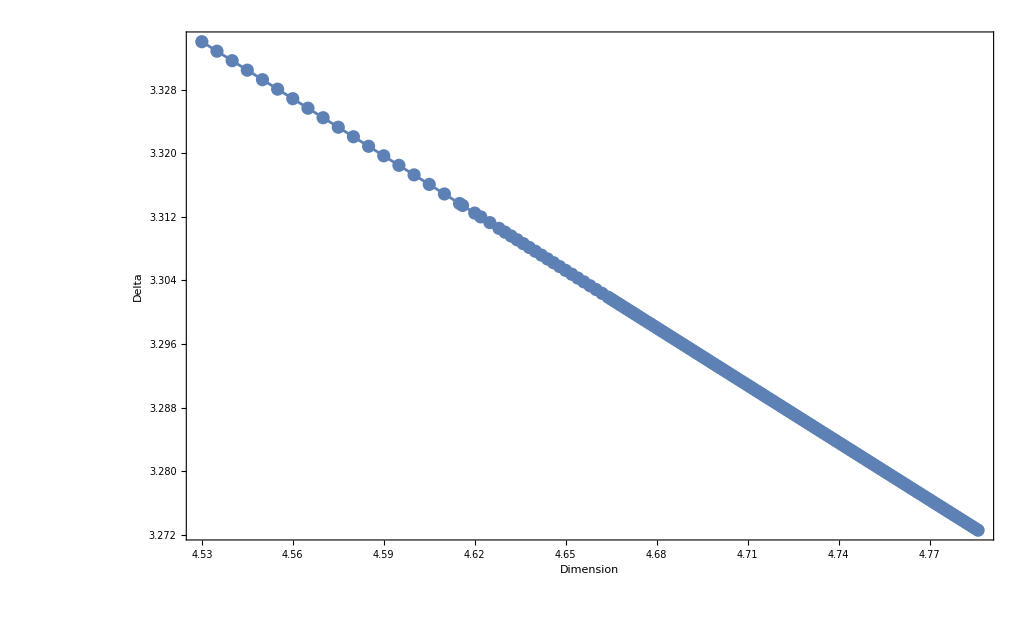

```mathematica
p1=Show[
ListPlot[Drop[Union[SortBy[Flatten[DeltaListAll,1],First]][[45;;]],-1],Joined->True,Mesh->All,PlotRange->All,Frame->True,FrameLabel->{"Dimension","Delta"},LabelStyle->Directive[16,Black],ImageSize->500],
Plot[fit/.sol,{x,4.7,4.76},PlotStyle->Red],PlotRange->{{4.7,4.8},{3.29,3.27}}
]
```

```mathematica
Export["linearDelta.pdf",p1]
```

linearDelta.pdf

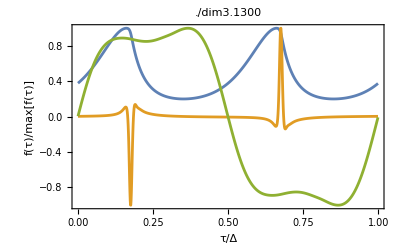
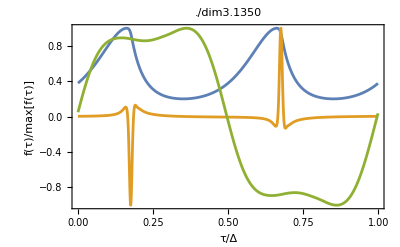
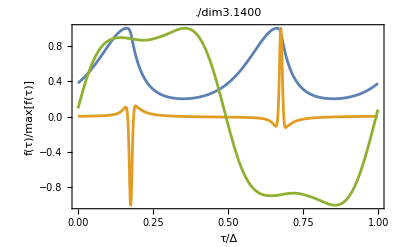
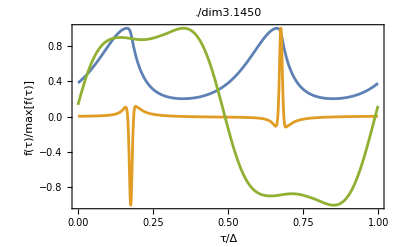
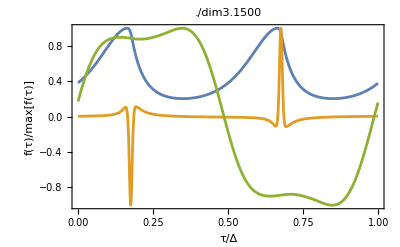
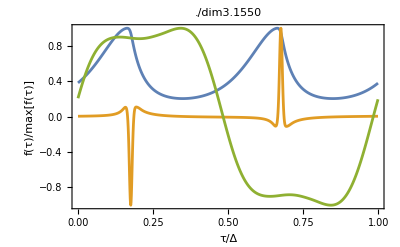
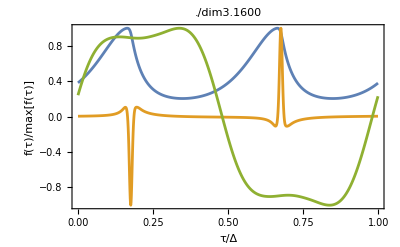
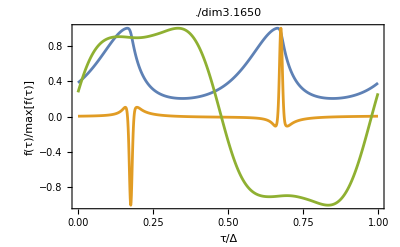
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotListAll[[1]]
```

```mathematica
plotListAll[[1]][[60]]
```

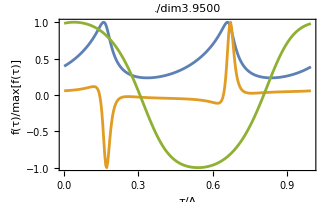

```mathematica
ListAnimate[plotListAll[[1]][[;;]]]
```

{a_1,a_2,a_3,a_4,a_5,a_6}

{a_1→18.6041,a_2→-44.823,a_3→30.4904,a_4→90.2381,a_5→-194.914,a_6→111.148}

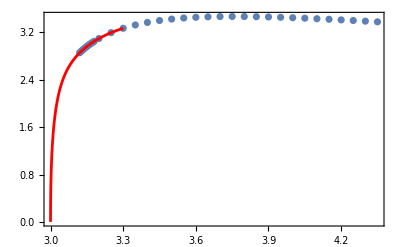

0.

```mathematica
data=DeltaListAll[[3,20;;24]];
(*ffit[x_]:=a+b*x+c*x^2+d x^3*)
ffit[x_]:=Sum[Subscript[a, n](x-3)^(n/2),{n,1,6}]
coeffs=Table[Subscript[a, n],{n,6}]
fit=FindFit[data,ffit[x],coeffs,x]
(*fit=FindFit[data,ffit[x],{a,b,c,d,e},x]*)
Show[
ListPlot[DeltaListAll[[3,8;;]],Frame->True,PlotRange->All],
Plot[ffit[x]/.fit,{x,3,data[[-1,1]]},PlotStyle->Red,PlotRange->All]
,PlotRange->All
]
ffit[x]/.fit/.x->3
```

```mathematica
SortBy[DeltaListAll[[3,8;;]],Last]
```

{{3.12,2.85383},{3.125,2.87338},{3.13,2.89214},{3.135,2.91016},{3.14,2.92749},{3.145,2.94418},{3.15,2.96028},{3.155,2.9758},{3.16,2.9908},{3.165,3.00529},{3.17,3.0193},{3.175,3.03286},{3.18,3.04599},{3.2,3.09452},{3.25,3.1931},{3.3,3.26719},{3.35,3.32346},{3.4,3.36625},{4.35,3.3761},{4.3,3.38734},{4.25,3.39827},{3.45,3.39862},{4.2,3.40884},{4.15,3.41895},{3.5,3.42279},{4.1,3.4285},{4.05,3.43738},{3.55,3.4404},{4.,3.44545},{3.95,3.45255},{3.6,3.45272},{3.9,3.45849},{3.65,3.46073},{3.85,3.46303},{3.7,3.4652},{3.8,3.4659},{3.75,3.46676},{3.115,$Failed}}

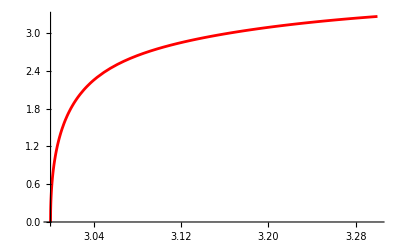

```mathematica
Plot[ffit[x]/.fit,{x,3,data[[-1,1]]},PlotStyle->Red,PlotRange->All]
```

```mathematica
FindRoot[D[Interpolation[DeltaListAll[[1]]][x],x],{x,3.5}]
FindRoot[D[Interpolation[DeltaListAll[[2]]][x],x],{x,3.5}]
FindRoot[D[Interpolation[DeltaListAll[[3]]][x],x],{x,3.5}]
```

{x→3.75585}

{x→3.75585}

{x→3.75585}

```mathematica
data
```

{{3.175,3.03286},{3.18,3.04599},{3.2,3.09452},{3.25,3.1931},{3.3,3.26719}}

InterpolatingFunction[…]

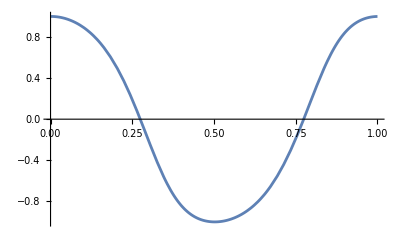

```mathematica
UpInt=Interpolation[UpNow]
Plot[UpInt[x],{x,0,1}]
```

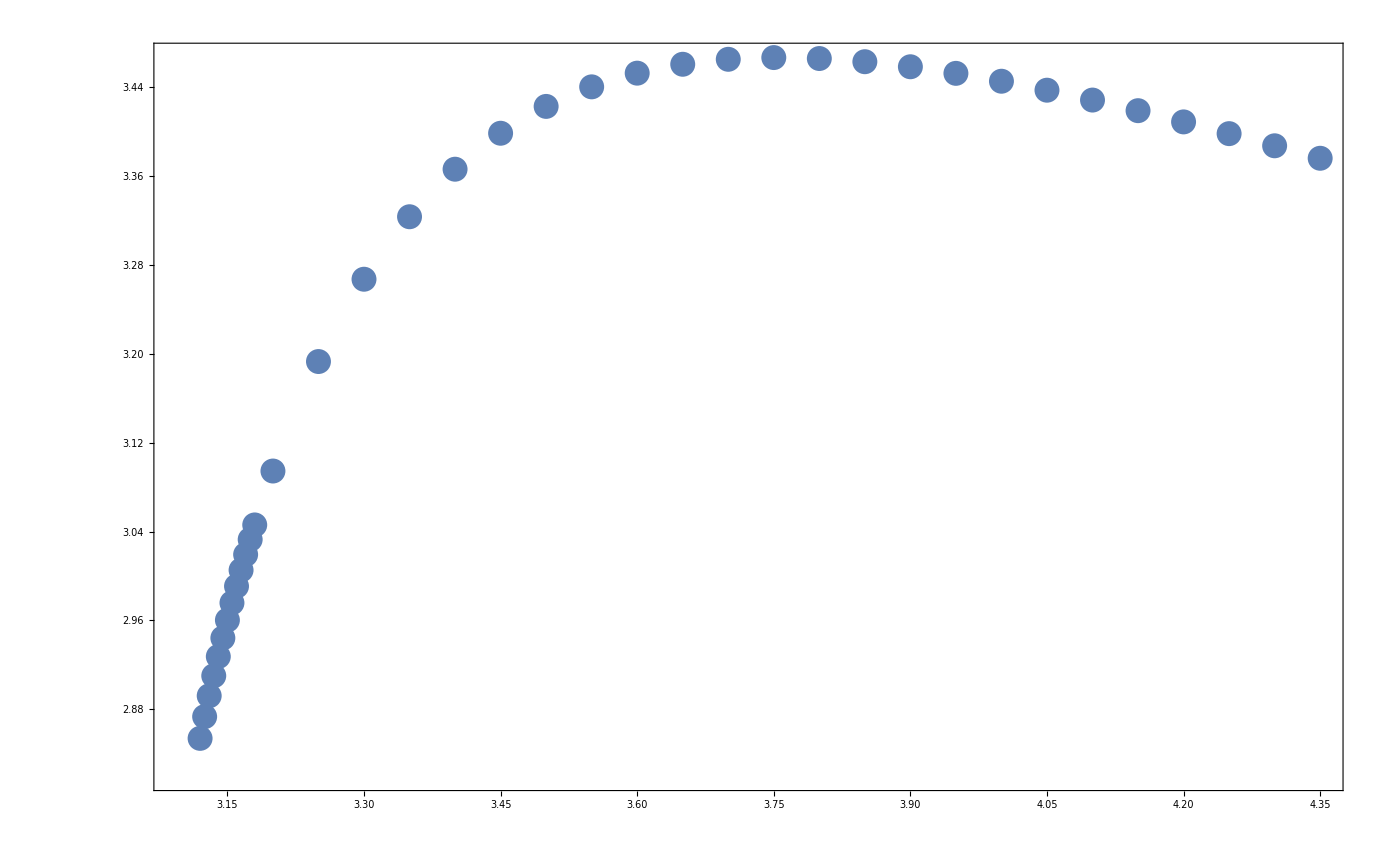

```mathematica
ListPlot[DeltaListAll[[3,9;;]],Frame->True,PlotRange->All]
```

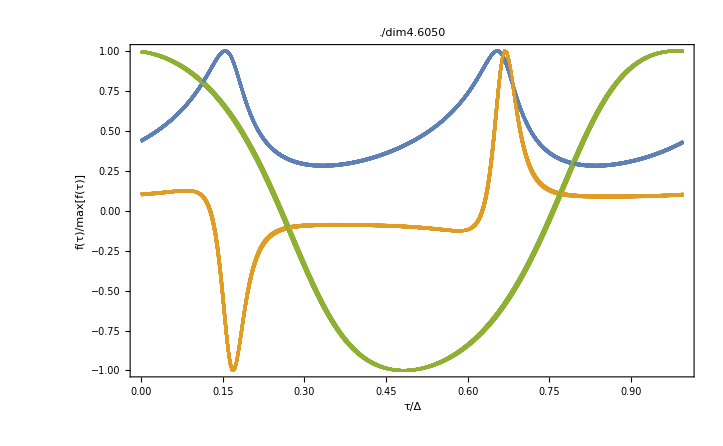

```mathematica
Show[plotListAll[[1,60;;]],PlotRange->All]
```

```mathematica
p1=Table[{plotListAll[[1,i]],plotListAll[[2,i]],plotListAll[[3,i]]},{i,Length[plotListAll[[1]]]}]
```

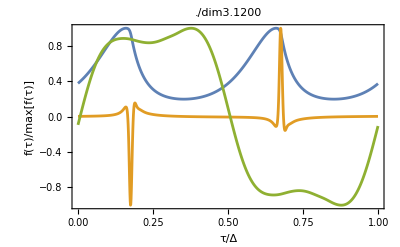
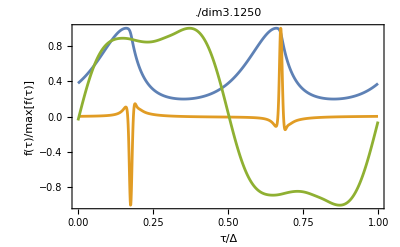
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotListAll[[3,9;;]]
```

```mathematica
ListAnimate[plotListAll[[3,9;;]]]
```

### Mode extension (single files)

```mathematica
NotebookDirectory[]
```

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/

```mathematica
(* looping over Mathematica files *)
SetDirectory[NotebookDirectory[]];
<<"fourdiff.wl"
(* available mathematica solutions *)
mFile="./DscanMathematica128/dim3.1150new2.res"
```

./DscanMathematica128/dim3.1150new2.res

```mathematica
X=Get[mFile][[-1]]//N;
Nt=Length[X[[3]]]*4;
Delta=X[[-1,1]];
```

```mathematica
(* building complex modes *)
fcmodes=X[[1]]+I*X[[2]];
Psicmodes=X[[3]]+I*X[[4]];
upmodes=X[[5]]+I*X[[6]];
fcFourier=Riffle[Join[fcmodes,Reverse[Conjugate[fcmodes[[2;;-2]]]]],0,{2,-1,2}];
PsicFourier=Riffle[Join[Psicmodes,Reverse[Conjugate[Psicmodes]]],0,{1,-2,2}];
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
```

```mathematica
(* double modes *)
fcFourierdoub=double[fcFourier,Nt];
PsicFourierdoub=double[PsicFourier,Nt];
upFourierdoub=double[upFourier,Nt];
{fclistdoub,psiclistdoub,uplistdoub}=Re@(Sqrt[2Nt]InverseFourier/@{fcFourierdoub,PsicFourierdoub,upFourierdoub});
```

```mathematica
(* exporting Fortan parameter files *)
Export["fc.dat",fclistdoub];
Export["psic.dat",psiclistdoub];
Export["Up.dat",uplistdoub];
Export["Delta.dat",Delta];
```

```mathematica
(* extending to 256 modes *)
nModes=256;
fclistdoub=Import["fc.dat"]//Flatten;
psiclistdoub=Import["psic.dat"]//Flatten;
uplistdoub=Import["Up.dat"]//Flatten;
Delta=Import["Delta.dat"];
(* doubling modes *)
fclistdoub2=Re[√(nModes*2)InverseFourier[double[Fourier[fclistdoub]/√nModes,nModes]]];
psiclistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[psiclistdoub]/√nModes,nModes]]];
uplistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[uplistdoub]/√nModes,nModes]]];
```

```mathematica
(* exporting Fortan parameter files *)
Export["fc.dat",fclistdoub2];
Export["psic.dat",psiclistdoub2];
Export["Up.dat",uplistdoub2];
Export["Delta.dat",Delta];
```

### Simulation Directories for D scan around max Delta

```mathematica
(* dimensions *)
dims=Join[Range[3.71,3.74,0.01],Range[3.76,3.79,0.01]]
```

{3.71,3.72,3.73,3.74,3.76,3.77,3.78,3.79}

```mathematica
(* new simulation directory names *)
dirNames=Table["dim"<>ToString[NumberForm[dims[[i]],{5,4}]]<>"/512",{i,Length[dims]}]
```

{dim3.7100/512,dim3.7200/512,dim3.7300/512,dim3.7400/512,dim3.7600/512,dim3.7700/512,dim3.7800/512,dim3.7900/512}

```mathematica
runFile=Import["template/run.sh","Table"]
```

{{#!/bin/bash},{#SBATCH,--ntasks=1},{#SBATCH,--nodes=1},{#SBATCH,--cpus-per-task=1},{#SBATCH,--job-name="CritD<4"},{#SBATCH,--partition=calea},{##SBATCH,--partition=iboga},{#SBATCH,--time=96:00:00},{#SBATCH,--output=run.log},{#SBATCH,--mail-type=ALL},{#SBATCH,--mail-user=ecker@itp.uni-frankfurt.de},{},{./shoot_inner.exe,>,shoot_inner.log}}

```mathematica
parFile=Import["template/shoot_inner.par","Table"];
(* setting number of modes *)
parFile[[1,1]]=1024
(* setting resolution *)
parFile[[11,1]]=4000
parFile[[12,1]]=4000
parFile
```

1024

4000

4000

```mathematica
parFile[[2,1]]=dims[[1]]
```

3.71

```mathematica
CreateDirectory[dirNames[[1]]]
```

CreateDirectory::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512 already exists.

$Failed

```mathematica
CopyFile["./dim3.7500/512/Delta.dat",dirNames[[1]]<>"/Delta.dat",OverwriteTarget->True]
CopyFile["./dim3.7500/512/fc.dat",dirNames[[1]]<>"/fc.dat",OverwriteTarget->True]
CopyFile["./dim3.7500/512/grid.dat",dirNames[[1]]<>"/grid.dat",OverwriteTarget->True]
CopyFile["./dim3.7500/512/psic.dat",dirNames[[1]]<>"/psic.dat",OverwriteTarget->True]
```

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512/Delta.dat

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512/fc.dat

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512/grid.dat

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512/psic.dat

```mathematica
(* creating simulation directories for 128 modes in Fortran startng with 128 mode solution in Mathematica *)
SetDirectory[NotebookDirectory[]];
Do[
(* creating Fortran simulation directory *)
CreateDirectory[dirNames[[i]]]//Quiet;
(* copy initial files for given dimension into new simulation directory *)
CopyFile["./dim3.7500/512/Delta.dat",dirNames[[i]]<>"/Delta.dat",OverwriteTarget->True];
CopyFile["./dim3.7500/512/fc.dat",dirNames[[i]]<>"/fc.dat",OverwriteTarget->True];
CopyFile["./dim3.7500/512/grid.dat",dirNames[[i]]<>"/grid.dat",OverwriteTarget->True];
CopyFile["./dim3.7500/512/psic.dat",dirNames[[i]]<>"/psic.dat",OverwriteTarget->True];
CopyFile["./dim3.7500/512/Up.dat",dirNames[[i]]<>"/Up.dat",OverwriteTarget->True];
(* updating dimension in parameter file *)
parFile[[2,1]]=dims[[i]];
Export[dirNames[[i]]<>"/shoot_inner.par",parFile,"Table"];
(* updating job name in parameter file *)
runFile[[5,2]]="--job-name=\"512d"<>ToString[dims[[i]]]<>"\"";
Export[dirNames[[i]]<>"/run.sh",runFile,"Table"];
(* copying code into simulation directory *)
CopyFile["template/shoot_inner.exe",dirNames[[i]]<>"/shoot_inner.exe"];
,{i,Length[dirNames]}]
```

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7100/512/shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7200/512/shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.7300/512/shoot_inner.exe already exists.

General::stop: Further output of CopyFile::eexist will be suppressed during this calculation.

```mathematica
(* available result directories *)
dirNames={"./dim3.7100","./dim3.7400","./dim3.7500","./dim3.7550","./dim3.7554","./dim3.7555","./dim3.7556","./dim3.7557","./dim3.75572","./dim3.755726","./dim3.7557262","./dim3.75572621","./dim3.75572622","./dim3.75572623","./dim3.75573","./dim3.7558","./dim3.7559","./dim3.7560","./dim3.7600","./dim3.7900","./dim3.8000"}
```

{./dim3.7100,./dim3.7400,./dim3.7500,./dim3.7550,./dim3.7554,./dim3.7555,./dim3.7556,./dim3.7557,./dim3.75572,./dim3.755726,./dim3.7557262,./dim3.75572621,./dim3.75572622,./dim3.75572623,./dim3.75573,./dim3.7558,./dim3.7559,./dim3.7560,./dim3.7600,./dim3.7900,./dim3.8000}

```mathematica
(* plotting results *)
SetDirectory[NotebookDirectory[]]
ModeList={512};
plotListAll={};
DeltaListAll={};
Monitor[
Do[
plotList={};
DeltaList={};
nModes=ModeList[[j]];
Do[
dimNow=Import[dirNames[[k]]<>"/"<>ToString[nModes]<>"/shoot_inner.par","Table"][[2,1]];
dirNow=dirNames[[k]]<>"/"<>ToString[nModes];
fclist=Import[dirNow<>"/fc.out"]//Flatten;
psiclist=Import[dirNow<>"/psic.out"]//Flatten;
Uplist=Import[dirNow<>"/Up.out"]//Flatten;
Delta=ToExpression[Import[dirNow<>"/Delta.out"]];
fcNow=Table[{(i-1)/(2*nModes),fclist[[i]]/Max[fclist]},{i,nModes*2}];
psicNow=Table[{(i-1)/(2*nModes),psiclist[[i]]/Max[psiclist]},{i,nModes*2}];
UpNow=Table[{(i-1)/(2*nModes),Uplist[[i]]/Max[Uplist]},{i,nModes*2}];
pNow=ListPlot[{fcNow,psicNow,UpNow},Joined->True,PlotRange->All,Frame->True,PlotLabel->dirNames[[k]],FrameLabel->{"τ/Δ","f(τ)/max[f(τ)]"}];
AppendTo[plotList,pNow];
AppendTo[DeltaList,{dimNow,Delta}];
,{k,Length[dirNames]}];
AppendTo[DeltaListAll,DeltaList];
AppendTo[plotListAll,plotList];
,{j,Length[ModeList]}]
,{j,k}]
```

/home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran

```mathematica
plotListAll
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
pList=SortBy[Flatten[DeltaListAll,1],First];
const=Max[pList[[;;,2]]]
pListsub=Thread[{pList[[;;,1]],const-pList[[;;,2]]+1}]
```

3.46677

{{3.71,1.00104},{3.74,1.00012},{3.75,1.00002},{3.755,1.},{3.7554,1.},{3.7555,1.},{3.7556,1.},{3.7557,1.},{3.75572,1.},{3.75573,1.},{3.75573,1.},{3.75573,1.},{3.75573,1.},{3.75573,1.},{3.75573,1.},{3.7558,1.},{3.7559,1.},{3.756,1.},{3.76,1.00001},{3.79,1.00053},{3.8,1.00088}}

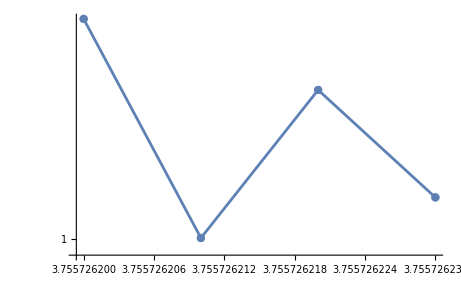

```mathematica
ListLogPlot[pListsub[[11;;-8]],PlotRange->All,Joined->True,InterpolationOrder->1,Mesh->Full]
```

```mathematica
FindMaximum[Interpolation[pList[[5;;-5]]][x],{x,3.7557}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.46677,{x→3.75572}}

```mathematica
DeltaInt=Interpolation[pList[[5;;-5]],InterpolationOrder->2]
```

InterpolatingFunction[…]

FittedModel[…]

{a→2.88898,b→0.307688,c→-0.0409625}

{{4.00425×10^-14,7.22552×10^-14,-2.20775×10^-14},{7.22552×10^-14,1.30382×10^-13,-3.98379×10^-14},{-2.20775×10^-14,-3.98379×10^-14,1.21724×10^-14}}

{2.00106×10^-7,3.61084×10^-7,1.10329×10^-7}

3.75573

3.46677

{1,3.75573,14.1055}

{2.01095×10^-13}

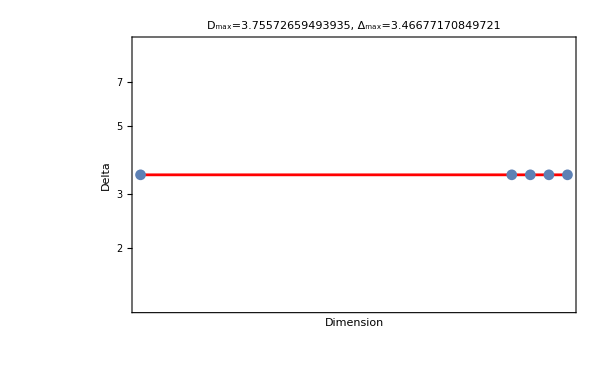

```mathematica
data=pList[[10;;-8]];
ffit[x_]:=a+b*x+c*x^2(*+d x^3*)
fit=NonlinearModelFit[data,ffit[x],{a,b,c},x]
bestFitParams=fit["BestFitParameters"]
covarianceMatrix=fit["CovarianceMatrix"]
parameterErrors=Sqrt[Diagonal[covarianceMatrix]]
Dmax=x/.Solve[0==ffit'[x]/.bestFitParams][[1]]
DeltaMax=ffit[x]/.bestFitParams/.x->Dmax
gradient=D[ffit[x],{{a,b,c}}]/. x->Dmax
errorAtDmax=Sqrt[gradient.covarianceMatrix.Transpose[{gradient}]]
Show[
LogLogPlot[ffit[x]/.bestFitParams,{x,data[[1,1]],data[[-1,1]]},PlotStyle->Red,PlotRange->All,GridLines->{{{Dmax,Black}},None},Frame->True,LabelStyle->Directive[12,Black],ImageSize->600,FrameLabel->{"Dimension","Delta"},
PlotLabel->"D_max="<>ToString[NumberForm[Dmax,{16,14}]]<>", Δ_max="<>ToString[NumberForm[DeltaMax,{16,14}]]
],
ListLogLogPlot[data[[;;]]]
]
```

```mathematica
pList//TableForm
```

3.71 | 3.46573
3.74 | 3.46665
3.75 | 3.46676
3.755 | 3.46677
3.7554 | 3.46677
3.7555 | 3.46677
3.7556 | 3.46677
3.7557 | 3.46677
3.75572 | 3.46677
3.75573 | 3.46677
3.75573 | 3.46677
3.75573 | 3.46677
3.75573 | 3.46677
3.75573 | 3.46677
3.75573 | 3.46677
3.7558 | 3.46677
3.7559 | 3.46677
3.756 | 3.46677
3.76 | 3.46676
3.79 | 3.46624
3.8 | 3.4659

```mathematica
{{3.71, 3.465727365699488}, {3.7399999999999998, 3.466652801443328}, {3.75, 3.466756139334302}, {3.755, 3.466771459633209}, {3.7554, 3.466771658306713}, {3.7555, 3.466771684364778}, {3.7556, 3.466771700985632}, {3.7557, 3.466771708172746}, {3.75572, 3.466771708479125}, {3.755726, 3.466771708497207}, {3.7557262, 3.46677170849712}, {3.75572621, 3.466771708497283}, {3.75572622, 3.466771708497173}, {3.75572623, 3.466771708497253}, {3.75573, 3.466771708490644}, {3.7558, 3.466771705930761}, {3.7559, 3.466771694261722}, {3.756, 3.466771673170357}, {3.76, 3.466763142673644}, {3.7899999999999996, 3.466240629926943}, {3.8, 3.465896108512275}}
```

{{3.71,3.46573},{3.74,3.46665},{3.75,3.46676},{3.755,3.46677},{3.7554,3.46677},{3.7555,3.46677},{3.7556,3.46677},{3.7557,3.46677},{3.75572,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.7558,3.46677},{3.7559,3.46677},{3.756,3.46677},{3.76,3.46676},{3.79,3.46624},{3.8,3.4659}}

```mathematica
NumberForm[Dmax,{18,18}]
```

3.755757595511457000

```mathematica
data
```

{{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677},{3.75573,3.46677}}

```mathematica
{{3.755726    ,3.466771708497207},
{3.7557262  ,3.46677170849712},
{3.75572622,3.466771708497173},
{3.75572623,3.466771708497253}}
```

```mathematica
3.46677170849712
```

```mathematica
3.466771708497283
```

```mathematica
3.466771708497173
```

```mathematica
data
```

```mathematica
NumberForm[data,{16,16}]
```

{{3.7557262000000000,3.4667717084971200},{3.7557262100000000,3.4667717084972830},{3.7557262200000000,3.4667717084971730}}

```mathematica
data
```

```mathematica
Eigenvalues[covarianceMatrix]
```

{0.0000124622,2.73338×10^-18,-6.80738×10^-23}

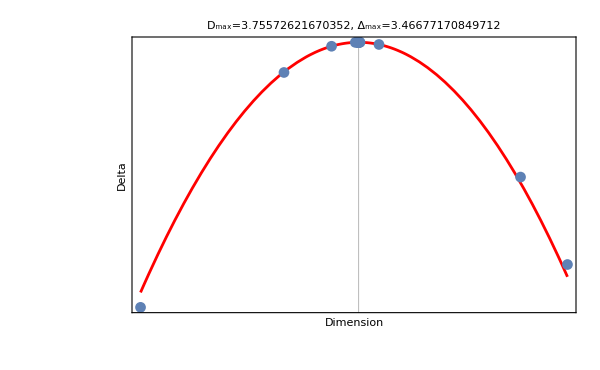

```mathematica
Show[
LogLogPlot[ffit[x]/.bestFitParams,{x,pList[[1,1]],pList[[-1,1]]},PlotStyle->Red,PlotRange->All,GridLines->{{{Dmax,Black}},None},Frame->True,LabelStyle->Directive[12,Black],ImageSize->600,FrameLabel->{"Dimension","Delta"},
PlotLabel->"D_max="<>ToString[NumberForm[Dmax,{16,14}]]<>", Δ_max="<>ToString[NumberForm[DeltaMax,{16,14}]]
],
ListLogLogPlot[pList],PlotRange->All
]
```

### Simulation Directories for D scan between D=4.3500 up to D=5

```mathematica
(* looping over Mathematica files *)
SetDirectory[NotebookDirectory[]];
<<"fourdiff.wl"
(* available mathematica solutions *)
mFiles=FileNames["./DscanMathematica128/*"][[49;;]]
```

{./DscanMathematica128/dim4.3550.res,./DscanMathematica128/dim4.3600.res,./DscanMathematica128/dim4.3650.res,./DscanMathematica128/dim4.3700.res,./DscanMathematica128/dim4.3750.res,./DscanMathematica128/dim4.3800.res,./DscanMathematica128/dim4.3850.res,./DscanMathematica128/dim4.3900.res,./DscanMathematica128/dim4.3950.res,./DscanMathematica128/dim4.4000.res,./DscanMathematica128/dim4.4050.res,./DscanMathematica128/dim4.4100.res,./DscanMathematica128/dim4.4150.res,./DscanMathematica128/dim4.4200.res,./DscanMathematica128/dim4.4250.res,./DscanMathematica128/dim4.4300.res,./DscanMathematica128/dim4.4350.res,./DscanMathematica128/dim4.4400.res,./DscanMathematica128/dim4.4450.res,./DscanMathematica128/dim4.4500.res,./DscanMathematica128/dim4.4550.res,./DscanMathematica128/dim4.4600.res,./DscanMathematica128/dim4.4650.res,./DscanMathematica128/dim4.4700.res,./DscanMathematica128/dim4.4750.res,./DscanMathematica128/dim4.4800.res,./DscanMathematica128/dim4.4850.res,./DscanMathematica128/dim4.4900.res,./DscanMathematica128/dim4.4950.res,./DscanMathematica128/dim4.5000.res,./DscanMathematica128/dim4.5050.res,./DscanMathematica128/dim4.5100.res,./DscanMathematica128/dim4.5150.res,./DscanMathematica128/dim4.5200.res,./DscanMathematica128/dim4.5250.res,./DscanMathematica128/dim4.5300.res,./DscanMathematica128/dim4.5350.res,./DscanMathematica128/dim4.5400.res,./DscanMathematica128/dim4.5450.res,./DscanMathematica128/dim4.5500.res,./DscanMathematica128/dim4.5550.res,./DscanMathematica128/dim4.5600.res,./DscanMathematica128/dim4.5650.res,./DscanMathematica128/dim4.5700.res,./DscanMathematica128/dim4.5750.res,./DscanMathematica128/dim4.5800.res,./DscanMathematica128/dim4.5850.res,./DscanMathematica128/dim4.5900.res,./DscanMathematica128/dim4.5950.res,./DscanMathematica128/dim4.6000.res,./DscanMathematica128/dim4.6050.res,./DscanMathematica128/dim4.6100.res,./DscanMathematica128/dim4.6150.res,./DscanMathematica128/dim4.6200.res,./DscanMathematica128/dim4.6250.res}

```mathematica
(* file names *)
mFileNames=Table[StringDrop[mFiles[[i]],22],{i,Length[mFiles]}]
```

{dim4.3550.res,dim4.3600.res,dim4.3650.res,dim4.3700.res,dim4.3750.res,dim4.3800.res,dim4.3850.res,dim4.3900.res,dim4.3950.res,dim4.4000.res,dim4.4050.res,dim4.4100.res,dim4.4150.res,dim4.4200.res,dim4.4250.res,dim4.4300.res,dim4.4350.res,dim4.4400.res,dim4.4450.res,dim4.4500.res,dim4.4550.res,dim4.4600.res,dim4.4650.res,dim4.4700.res,dim4.4750.res,dim4.4800.res,dim4.4850.res,dim4.4900.res,dim4.4950.res,dim4.5000.res,dim4.5050.res,dim4.5100.res,dim4.5150.res,dim4.5200.res,dim4.5250.res,dim4.5300.res,dim4.5350.res,dim4.5400.res,dim4.5450.res,dim4.5500.res,dim4.5550.res,dim4.5600.res,dim4.5650.res,dim4.5700.res,dim4.5750.res,dim4.5800.res,dim4.5850.res,dim4.5900.res,dim4.5950.res,dim4.6000.res,dim4.6050.res,dim4.6100.res,dim4.6150.res,dim4.6200.res,dim4.6250.res}

```mathematica
(* new simulation directory names *)
dirNames=Table[StringDrop[mFileNames[[i]],-4],{i,Length[mFileNames]}]
```

{dim4.3550,dim4.3600,dim4.3650,dim4.3700,dim4.3750,dim4.3800,dim4.3850,dim4.3900,dim4.3950,dim4.4000,dim4.4050,dim4.4100,dim4.4150,dim4.4200,dim4.4250,dim4.4300,dim4.4350,dim4.4400,dim4.4450,dim4.4500,dim4.4550,dim4.4600,dim4.4650,dim4.4700,dim4.4750,dim4.4800,dim4.4850,dim4.4900,dim4.4950,dim4.5000,dim4.5050,dim4.5100,dim4.5150,dim4.5200,dim4.5250,dim4.5300,dim4.5350,dim4.5400,dim4.5450,dim4.5500,dim4.5550,dim4.5600,dim4.5650,dim4.5700,dim4.5750,dim4.5800,dim4.5850,dim4.5900,dim4.5950,dim4.6000,dim4.6050,dim4.6100,dim4.6150,dim4.6200,dim4.6250}

```mathematica
(* extracting dimension from file names, not ideal, should be stored in result files *)
dimList=Table[StringDrop[dirNames[[i]],3],{i,Length[dirNames]}]
```

{4.3550,4.3600,4.3650,4.3700,4.3750,4.3800,4.3850,4.3900,4.3950,4.4000,4.4050,4.4100,4.4150,4.4200,4.4250,4.4300,4.4350,4.4400,4.4450,4.4500,4.4550,4.4600,4.4650,4.4700,4.4750,4.4800,4.4850,4.4900,4.4950,4.5000,4.5050,4.5100,4.5150,4.5200,4.5250,4.5300,4.5350,4.5400,4.5450,4.5500,4.5550,4.5600,4.5650,4.5700,4.5750,4.5800,4.5850,4.5900,4.5950,4.6000,4.6050,4.6100,4.6150,4.6200,4.6250}

```mathematica
parFile=Import["template/shoot_inner.par","Table"]
```

{{256,ny,,doubled,modes},{3.5,dim},{0.001,xleft},{0.1,xmid},{0.999,xright},{1.×10^-8,eps},{1.×10^-14,errmax,,precision,of,outer,Newton},{T,verbose},{0.001,slowerr},{0,outevery},{3000,nleft},{3000,nright},{1.,refine},{2,method},{1.×10^-15,crit,,precision,of,implicit,solver},{F,debug}}

```mathematica
runFile=Import["template/run.sh","Table"]
```

{{#!/bin/bash},{#SBATCH,--ntasks=1},{#SBATCH,--nodes=1},{#SBATCH,--cpus-per-task=1},{#SBATCH,--job-name="CritD<4"},{#SBATCH,--partition=calea},{##SBATCH,--partition=iboga},{#SBATCH,--time=96:00:00},{#SBATCH,--output=run.log},{#SBATCH,--mail-type=ALL},{#SBATCH,--mail-user=ecker@itp.uni-frankfurt.de},{},{./shoot_inner.exe,>,shoot_inner.log}}

```mathematica
(* creating simulation directories for 128 modes in Fortran startng with 128 mode solution in Mathematica *)
SetDirectory[NotebookDirectory[]];
Do[
(* creating Fortran simulation directory *)
CreateDirectory[dirNames[[i]]]//Quiet;
(* copy mathematica result for given dimension into new simulation directory *)
CopyFile[mFiles[[i]],dirNames[[i]]<>"/"<>mFileNames[[i]],OverwriteTarget->True];
(* loading mathematica result file *)
X=Get[mFiles[[i]]][[-1]]//N;
Nt=Length[X[[3]]]*4;
Delta=X[[-1,1]];
(* building complex modes *)
fcmodes=X[[1]]+I*X[[2]];
Psicmodes=X[[3]]+I*X[[4]];
upmodes=X[[5]]+I*X[[6]];
fcFourier=Riffle[Join[fcmodes,Reverse[Conjugate[fcmodes[[2;;-2]]]]],0,{2,-1,2}];
PsicFourier=Riffle[Join[Psicmodes,Reverse[Conjugate[Psicmodes]]],0,{1,-2,2}];
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
(* double modes *)
fcFourierdoub=double[fcFourier,Nt];
PsicFourierdoub=double[PsicFourier,Nt];
upFourierdoub=double[upFourier,Nt];
{fclistdoub,psiclistdoub,uplistdoub}=Re@(Sqrt[2Nt]InverseFourier/@{fcFourierdoub,PsicFourierdoub,upFourierdoub});
(* exporting Fortan parameter files *)
outDir=dirNames[[i]]<>"/128/";
CreateDirectory[outDir]//Quiet;
Export[outDir<>"fc.dat",fclistdoub];
Export[outDir<>"psic.dat",psiclistdoub];
Export[outDir<>"Up.dat",uplistdoub];
Export[outDir<>"Delta.dat",Delta];
(* updating dimension in parameter file *)
parFile[[2,1]]=dimList[[i]];
Export[outDir<>"/shoot_inner.par",parFile,"Table"];
(* updating job name in parameter file *)
runFile[[5,2]]="--job-name=\""<>dimList[[i]]<>"\"";
Export[outDir<>"/run.sh",runFile,"Table"];
(* copying code into simulation directory *)
CopyFile["template/shoot_inner.exe",outDir<>"/shoot_inner.exe"];
,{i,Length[dirNames]}]
```

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim4.3550/128//shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim4.3600/128//shoot_inner.exe already exists.

```mathematica
(* bash script for submiting sequential jobs *)
```

### Mode extension (many files)

```mathematica
(* looping over Mathematica files *)
SetDirectory[NotebookDirectory[]];
<<"fourdiff.wl"
(* available mathematica solutions *)
mFiles=FileNames["./DscanMathematica128/*"]
```

{./DscanMathematica128/dim3.0850.res,./DscanMathematica128/dim3.0875.res,./DscanMathematica128/dim3.0900.res,./DscanMathematica128/dim3.0925.res,./DscanMathematica128/dim3.0950.res,./DscanMathematica128/dim3.0975.res,./DscanMathematica128/dim3.1000.res,./DscanMathematica128/dim3.1050.res,./DscanMathematica128/dim3.1100.res,./DscanMathematica128/dim3.1150.res,./DscanMathematica128/dim3.1200.res,./DscanMathematica128/dim3.1250.res,./DscanMathematica128/dim3.1300.res,./DscanMathematica128/dim3.1350.res,./DscanMathematica128/dim3.1400.res,./DscanMathematica128/dim3.1450.res,./DscanMathematica128/dim3.1500.res,./DscanMathematica128/dim3.1550.res,./DscanMathematica128/dim3.1600.res,./DscanMathematica128/dim3.1650.res,./DscanMathematica128/dim3.1700.res,./DscanMathematica128/dim3.1750.res,./DscanMathematica128/dim3.1800.res,./DscanMathematica128/dim3.2000.res,./DscanMathematica128/dim3.2500.res,./DscanMathematica128/dim3.3000.res,./DscanMathematica128/dim3.3500.res,./DscanMathematica128/dim3.4000.res,./DscanMathematica128/dim3.4500.res,./DscanMathematica128/dim3.5000.res,./DscanMathematica128/dim3.5500.res,./DscanMathematica128/dim3.6000.res,./DscanMathematica128/dim3.6500.res,./DscanMathematica128/dim3.7000.res,./DscanMathematica128/dim3.7500.res,./DscanMathematica128/dim3.8000.res,./DscanMathematica128/dim3.8500.res,./DscanMathematica128/dim3.9000.res,./DscanMathematica128/dim3.9500.res,./DscanMathematica128/dim4.0000.res,./DscanMathematica128/dim4.0500.res,./DscanMathematica128/dim4.1000.res,./DscanMathematica128/dim4.1500.res,./DscanMathematica128/dim4.2000.res,./DscanMathematica128/dim4.2500.res,./DscanMathematica128/dim4.3000.res,./DscanMathematica128/dim4.3500.res}

```mathematica
FileNames["./dim*"]
```

{./dim3.0850,./dim3.0875,./dim3.0900,./dim3.0925,./dim3.0950,./dim3.0975,./dim3.1000,./dim3.1050,./dim3.1100,./dim3.1150,./dim3.1200,./dim3.1250,./dim3.1300,./dim3.1350,./dim3.1400,./dim3.1450,./dim3.1500,./dim3.1550,./dim3.1600,./dim3.1650,./dim3.1700,./dim3.1750,./dim3.1800,./dim3.2000,./dim3.2500,./dim3.3000,./dim3.3500,./dim3.4000,./dim3.4500,./dim3.5000,./dim3.5500,./dim3.6000,./dim3.6500,./dim3.7000,./dim3.7500,./dim3.8000,./dim3.8500,./dim3.9000,./dim3.9500,./dim4.0000,./dim4.0500,./dim4.1000,./dim4.1500,./dim4.2000,./dim4.2500,./dim4.3000,./dim4.3500}

```mathematica
(* file names *)
mFileNames=Table[StringDrop[mFiles[[i]],22],{i,Length[mFiles]}]
```

{dim3.0850.res,dim3.0875.res,dim3.0900.res,dim3.0925.res,dim3.0950.res,dim3.0975.res,dim3.1000.res,dim3.1050.res,dim3.1100.res,dim3.1150.res,dim3.1200.res,dim3.1250.res,dim3.1300.res,dim3.1350.res,dim3.1400.res,dim3.1450.res,dim3.1500.res,dim3.1550.res,dim3.1600.res,dim3.1650.res,dim3.1700.res,dim3.1750.res,dim3.1800.res,dim3.2000.res,dim3.2500.res,dim3.3000.res,dim3.3500.res,dim3.4000.res,dim3.4500.res,dim3.5000.res,dim3.5500.res,dim3.6000.res,dim3.6500.res,dim3.7000.res,dim3.7500.res,dim3.8000.res,dim3.8500.res,dim3.9000.res,dim3.9500.res,dim4.0000.res,dim4.0500.res,dim4.1000.res,dim4.1500.res,dim4.2000.res,dim4.2500.res,dim4.3000.res,dim4.3500.res}

```mathematica
(* new simulation directory names *)
dirNames=Table[StringDrop[mFileNames[[i]],-4],{i,Length[mFileNames]}]
```

{dim3.0850,dim3.0875,dim3.0900,dim3.0925,dim3.0950,dim3.0975,dim3.1000,dim3.1050,dim3.1100,dim3.1150,dim3.1200,dim3.1250,dim3.1300,dim3.1350,dim3.1400,dim3.1450,dim3.1500,dim3.1550,dim3.1600,dim3.1650,dim3.1700,dim3.1750,dim3.1800,dim3.2000,dim3.2500,dim3.3000,dim3.3500,dim3.4000,dim3.4500,dim3.5000,dim3.5500,dim3.6000,dim3.6500,dim3.7000,dim3.7500,dim3.8000,dim3.8500,dim3.9000,dim3.9500,dim4.0000,dim4.0500,dim4.1000,dim4.1500,dim4.2000,dim4.2500,dim4.3000,dim4.3500}

```mathematica
(* extracting dimension from file names, not ideal, should be stored in result files *)
dimList=Table[StringDrop[dirNames[[i]],3],{i,Length[dirNames]}]
```

{3.0850,3.0875,3.0900,3.0925,3.0950,3.0975,3.1000,3.1050,3.1100,3.1150,3.1200,3.1250,3.1300,3.1350,3.1400,3.1450,3.1500,3.1550,3.1600,3.1650,3.1700,3.1750,3.1800,3.2000,3.2500,3.3000,3.3500,3.4000,3.4500,3.5000,3.5500,3.6000,3.6500,3.7000,3.7500,3.8000,3.8500,3.9000,3.9500,4.0000,4.0500,4.1000,4.1500,4.2000,4.2500,4.3000,4.3500}

```mathematica
parFile=Import["template/shoot_inner.par","Table"]
```

{{256,ny,,doubled,modes},{3.5,dim},{0.001,xleft},{0.1,xmid},{0.999,xright},{1.×10^-8,eps},{1.×10^-14,errmax,,precision,of,outer,Newton},{T,verbose},{0.001,slowerr},{0,outevery},{3000,nleft},{3000,nright},{1.,refine},{2,method},{1.×10^-15,crit,,precision,of,implicit,solver},{F,debug}}

```mathematica
runFile=Import["template/run.sh","Table"]
```

{{#!/bin/bash},{#SBATCH,--ntasks=1},{#SBATCH,--nodes=1},{#SBATCH,--cpus-per-task=1},{#SBATCH,--job-name="CritD<4"},{#SBATCH,--partition=calea},{##SBATCH,--partition=iboga},{#SBATCH,--time=96:00:00},{#SBATCH,--output=run.log},{#SBATCH,--mail-type=ALL},{#SBATCH,--mail-user=ecker@itp.uni-frankfurt.de},{},{./shoot_inner.exe,>,shoot_inner.log}}

```mathematica
(* creating simulation directories for 128 modes in Fortran startng with 128 mode solution in Mathematica *)
SetDirectory[NotebookDirectory[]];
Do[
(* creating Fortran simulation directory *)
CreateDirectory[dirNames[[i]]]//Quiet;
(* copy mathematica result for given dimension into new simulation directory *)
CopyFile[mFiles[[i]],dirNames[[i]]<>"/"<>mFileNames[[i]],OverwriteTarget->True];
(* loading mathematica result file *)
X=Get[mFiles[[i]]][[-1]]//N;
Nt=Length[X[[3]]]*4;
Delta=X[[-1,1]];
(* building complex modes *)
fcmodes=X[[1]]+I*X[[2]];
Psicmodes=X[[3]]+I*X[[4]];
upmodes=X[[5]]+I*X[[6]];
fcFourier=Riffle[Join[fcmodes,Reverse[Conjugate[fcmodes[[2;;-2]]]]],0,{2,-1,2}];
PsicFourier=Riffle[Join[Psicmodes,Reverse[Conjugate[Psicmodes]]],0,{1,-2,2}];
upFourier=Riffle[Join[upmodes,Reverse[Conjugate[upmodes]]],0,{1,-2,2}];
(* double modes *)
fcFourierdoub=double[fcFourier,Nt];
PsicFourierdoub=double[PsicFourier,Nt];
upFourierdoub=double[upFourier,Nt];
{fclistdoub,psiclistdoub,uplistdoub}=Re@(Sqrt[2Nt]InverseFourier/@{fcFourierdoub,PsicFourierdoub,upFourierdoub});
(* exporting Fortan parameter files *)
outDir=dirNames[[i]]<>"/128/";
CreateDirectory[outDir]//Quiet;
Export[outDir<>"fc.dat",fclistdoub];
Export[outDir<>"psic.dat",psiclistdoub];
Export[outDir<>"Up.dat",uplistdoub];
Export[outDir<>"Delta.dat",Delta];
(* updating dimension in parameter file *)
parFile[[2,1]]=dimList[[i]];
Export[outDir<>"/shoot_inner.par",parFile,"Table"];
(* updating job name in parameter file *)
runFile[[5,2]]="--job-name=\"128d"<>dimList[[i]]<>"\"";
Export[outDir<>"/run.sh",runFile,"Table"];
(* copying code into simulation directory *)
CopyFile["template/shoot_inner.exe",outDir<>"/shoot_inner.exe"];
,{i,Length[dirNames]}]
```

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0850/128//shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0875/128//shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0900/128//shoot_inner.exe already exists.

General::stop: Further output of CopyFile::eexist will be suppressed during this calculation.

```mathematica
(* creating simulation directories for 256 modes in Fortran starting with 128 mode solution in Fortran *)
nModes=256;
Do[
(* importing 128 mode files *)
importDir=dirNames[[i]]<>"/128/";
fclistdoub=Import[importDir<>"fc.out"]//Flatten;
psiclistdoub=Import[importDir<>"psic.out"]//Flatten;
uplistdoub=Import[importDir<>"Up.out"]//Flatten;
Delta=Import[importDir<>"Delta.out"];
(* doubling modes *)
fclistdoub2=Re[√(nModes*2)InverseFourier[double[Fourier[fclistdoub]/√nModes,nModes]]];
psiclistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[psiclistdoub]/√nModes,nModes]]];
uplistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[uplistdoub]/√nModes,nModes]]];
(* updating dimension and mode number in parameter file *)
parFile[[2,1]]=dimList[[i]];
parFile[[1,1]]=nModes*2;
(* exporting Fortan parameter files *)
outDir=dirNames[[i]]<>"/256/";
CreateDirectory[outDir]//Quiet;
Export[outDir<>"fc.dat",fclistdoub2];
Export[outDir<>"psic.dat",psiclistdoub2];
Export[outDir<>"Up.dat",uplistdoub2];
Export[outDir<>"Delta.dat",Delta];
Export[outDir<>"shoot_inner.par",parFile,"Table"];
(* updating job name in parameter file *)
runFile[[5,2]]="--job-name=\"256d"<>dimList[[i]]<>"\"";
Export[outDir<>"/run.sh",runFile,"Table"];
(* copying code into simulation directory *)
CopyFile["template/shoot_inner.exe",outDir<>"/shoot_inner.exe"];
,{i,Length[dirNames]}]
```

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0900/256//shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0925/256//shoot_inner.exe already exists.

CopyFile::eexist: /home/ecker/Dropbox/CriticalCollapse/Code/NumericalProcedure/CE/Fortran/DscanFortran/dim3.0950/256//shoot_inner.exe already exists.

General::stop: Further output of CopyFile::eexist will be suppressed during this calculation.

```mathematica
p1=ListPlot[Re/@{fclistdoub,1/500 psiclistdoub,uplistdoub},Joined->True]
```

```mathematica
(* creating simulation directories for 512 modes in Fortran starting with 256 mode solution in Fortran *)
nModes=512;
Do[
(* importing 256 mode files *)
importDir=dirNames[[i]]<>"/256/";
fclistdoub=Import[importDir<>"fc.out"]//Flatten;
psiclistdoub=Import[importDir<>"psic.out"]//Flatten;
uplistdoub=Import[importDir<>"Up.out"]//Flatten;
Delta=Import[importDir<>"Delta.out"];
(* doubling modes *)
fclistdoub2=Re[√(nModes*2)InverseFourier[double[Fourier[fclistdoub]/√nModes,nModes]]];
psiclistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[psiclistdoub]/√nModes,nModes]]];
uplistdoub2=Re[√(2*nModes)InverseFourier[double[Fourier[uplistdoub]/√nModes,nModes]]];
(* updating dimension and mode number in parameter file *)
parFile[[2,1]]=dimList[[i]];
parFile[[1,1]]=nModes*2;
(* exporting Fortan parameter files *)
outDir=dirNames[[i]]<>"/512/";
CreateDirectory[outDir]//Quiet;
Export[outDir<>"fc.dat",fclistdoub2];
Export[outDir<>"psic.dat",psiclistdoub2];
Export[outDir<>"Up.dat",uplistdoub2];
Export[outDir<>"Delta.dat",Delta];
Export[outDir<>"shoot_inner.par",parFile,"Table"];
(* updating job name in parameter file *)
runFile[[5,2]]="--job-name=\"512d"<>dimList[[i]]<>"\"";
Export[outDir<>"/run.sh",runFile,"Table"];
(* copying code into simulation directory *)
CopyFile["template/shoot_inner.exe",outDir<>"/shoot_inner.exe"];
,{i,Length[dirNames]}]
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

Null

```mathematica
Null
```

```mathematica
parFile=Import["template/shoot_inner.par","Table"]
```

{{256,ny,,doubled,modes},{3.5,dim},{0.001,xleft},{0.1,xmid},{0.999,xright},{1.×10^-8,eps},{1.×10^-14,errmax,,precision,of,outer,Newton},{T,verbose},{0.001,slowerr},{0,outevery},{3000,nleft},{3000,nright},{1.,refine},{2,method},{1.×10^-15,crit,,precision,of,implicit,solver},{F,debug}}

```mathematica
(* increase number of x-points and overwrite par files for 512 modes *)
nModes=512;
pntsleft=4000;
pntsright=4000;
Do[
(* updating dimension and mode number in parameter file *)
parFile[[2,1]]=dimList[[i]];
parFile[[1,1]]=nModes*2;
parFile[[11,1]]=4000;
parFile[[12,1]]=4000;
(* exporting Fortan parameter files *)
outDir=dirNames[[i]]<>"/512/";
CreateDirectory[outDir]//Quiet;
Export[outDir<>"shoot_inner.par",parFile,"Table"];
,{i,Length[dirNames]}]
```